```mathematica
Manipulate[
Show[
ParametricPlot[{2Cos[2π s],2Sin[2π s]},{s,0,1}],
Graphics[{PointSize[0.03],Point[{2Sin[2π t^2],2Cos[2π t^2]}]}]
],
{t,0,1}
]
```

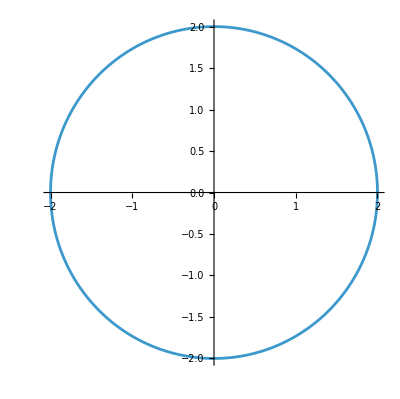

```mathematica
ParametricPlot[{2Cos[θ],2Sin[θ]},{θ,0,2π}]
```

```mathematica
Diameter[h_]:=4/7(7-h)
ParametricPlot3D[{Diameter[h]/2 Cos[θ],Diameter[h]/2 Sin[θ],h},{θ,0,2π},{h,0,7}]
```

-Graphics3D-

```mathematica
D[{Cos[6π t],Sin[8π t]},t]
```

{-6 π Sin[6 π t],8 π Cos[8 π t]}

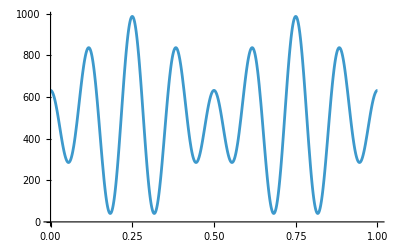

```mathematica
Plot[{-6 π Sin[6 π t],8 π Cos[8 π t]}.{-6 π Sin[6 π t],8 π Cos[8 π t]},{t,0,1}]
```

```mathematica
D[{-6 π Sin[6 π t],8 π Cos[8 π t]}.{-6 π Sin[6 π t],8 π Cos[8 π t]},t]
```

```mathematica
N[
Solve[432 π^3 Cos[6 π t] Sin[6 π t]-1024 π^3 Cos[8 π t] Sin[8 π t]==0&&0<=t<=1,t]
]
```

{{t→0.},{t→0.25},{t→0.5},{t→0.75},{t→1.},{t→0.94504},{t→0.0549599},{t→0.883225},{t→0.116775},{t→0.817313},{t→0.182687},{t→0.682687},{t→0.317313},{t→0.616775},{t→0.383225},{t→0.55496},{t→0.44504}}

```mathematica
{-6 π Sin[6 π t],8 π Cos[8 π t]}.{-6 π Sin[6 π t],8 π Cos[8 π t]}/.t->0.817313
```

40.6248

## Approximating π with a quadratic Bézier curve

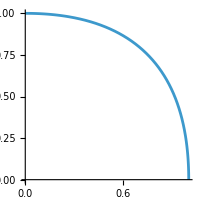

```mathematica
c[t_]:=(1-t)^2{1,0} + 2t(1-t){1,1}+t^2{0,1}
ParametricPlot[c[t],{t,0,1}]
```

```mathematica
D[c[t],t]
```

{-2 t,2 (1-t)}

```mathematica
Sqrt[{-2 t,2 (1-t)}.{-2 t,2 (1-t)}]
```

```mathematica
Integrate[√(4 (1-t)^2+4 t^2),{t,0,1}]
```

1+ArcSinh[1]/(√2)

```mathematica
1+ArcSinh[1]/(√2)//N
```

```mathematica
2*1.6232252401402305

N[π/2]
```

3.24645

1.5708

π

```mathematica
K=;
L=(4(-1+√2))/3;
c[t_]:=(1-t)^3{1,0} + 3t(1-t)^2{1,K}+3 t^2(1-t){K,1}+t^3{0,1}
2*NIntegrate[√(D[c[t],t].D[c[t],t]),{t,0,1}]
```

3.14171